# Числено решаване на обикновени диференциални уравнения

## Решение на втора задача

### а) Да се намери точното решение

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - 8Sin[x], y[x], x]
```

{{y[x]→ⅇ^x C[1]+4 (Cos[x]+Sin[x])}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - 8Sin[x], y[7] == 13}, y[x], x]
```

{{y[x]→(13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7}}

Визуализация на точното решение

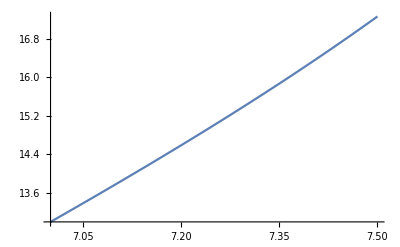

```mathematica
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
Plot[yt[x], {x, 7,7.5}]
```

### б) По метод на Рунге-Кута (1,1) да се реши приближено задачата със стъпка 0.025. Запишете резултатите в таблица.

#### 2.3. РК32 - Формула (1, 1)

Мрежата е с n = 20. и стъпка h = 0.025

Теоретичната локална грешка  е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 k_1 = 0.193603 k_2 = 0.194715 y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.025 y_i = 13.1942 f_i = 7.78914 k_1 = 0.194729 k_2 = 0.195953 y_точно = 13.1942 Истинска грешка = 2.366×10^-6

i = 2 x_i = 7.05 y_i = 13.3895 f_i = 7.83874 k_1 = 0.195969 k_2 = 0.197311 y_точно = 13.3895 Истинска грешка = 4.51419×10^-6

i = 3 x_i = 7.075 y_i = 13.5861 f_i = 7.8931 k_1 = 0.197328 k_2 = 0.198793 y_точно = 13.5861 Истинска грешка = 6.41306×10^-6

i = 4 x_i = 7.1 y_i = 13.7842 f_i = 7.95245 k_1 = 0.198811 k_2 = 0.200405 y_точно = 13.7842 Истинска грешка = 8.02983×10^-6

i = 5 x_i = 7.125 y_i = 13.9838 f_i = 8.01698 k_1 = 0.200425 k_2 = 0.202152 y_точно = 13.9838 Истинска грешка = 9.3305×10^-6

i = 6 x_i = 7.15 y_i = 14.1851 f_i = 8.08693 k_1 = 0.202173 k_2 = 0.204039 y_точно = 14.1851 Истинска грешка = 0.0000102797

i = 7 x_i = 7.175 y_i = 14.3882 f_i = 8.1625 k_1 = 0.204063 k_2 = 0.206073 y_точно = 14.3882 Истинска грешка = 0.0000108409

i = 8 x_i = 7.2 y_i = 14.5933 f_i = 8.24393 k_1 = 0.206098 k_2 = 0.208259 y_точно = 14.5933 Истинска грешка = 0.000010976

i = 9 x_i = 7.225 y_i = 14.8004 f_i = 8.33143 k_1 = 0.208286 k_2 = 0.210602 y_точно = 14.8004 Истинска грешка = 0.0000106456

i = 10 x_i = 7.25 y_i = 15.0099 f_i = 8.42524 k_1 = 0.210631 k_2 = 0.213109 y_точно = 15.0099 Истинска грешка = 9.80886×10^-6

i = 11 x_i = 7.275 y_i = 15.2218 f_i = 8.5256 k_1 = 0.21314 k_2 = 0.215785 y_точно = 15.2218 Истинска грешка = 8.42351×10^-6

i = 12 x_i = 7.3 y_i = 15.4362 f_i = 8.63273 k_1 = 0.215818 k_2 = 0.218637 y_точно = 15.4362 Истинска грешка = 6.44572×10^-6

i = 13 x_i = 7.325 y_i = 15.6535 f_i = 8.74688 k_1 = 0.218672 k_2 = 0.22167 y_точно = 15.6534 Истинска грешка = 3.83016×10^-6

i = 14 x_i = 7.35 y_i = 15.8736 f_i = 8.86829 k_1 = 0.221707 k_2 = 0.22489 y_точно = 15.8736 Истинска грешка = 5.29869×10^-7

i = 15 x_i = 7.375 y_i = 16.0969 f_i = 8.9972 k_1 = 0.22493 k_2 = 0.228305 y_точно = 16.0969 Истинска грешка = 3.5037×10^-6

i = 16 x_i = 7.4 y_i = 16.3235 f_i = 9.13387 k_1 = 0.228347 k_2 = 0.231919 y_точно = 16.3235 Истинска грешка = 8.32077×10^-6

i = 17 x_i = 7.425 y_i = 16.5537 f_i = 9.27855 k_1 = 0.231964 k_2 = 0.23574 y_точно = 16.5537 Истинска грешка = 0.0000139733

i = 18 x_i = 7.45 y_i = 16.7875 f_i = 9.4315 k_1 = 0.235787 k_2 = 0.239774 y_точно = 16.7875 Истинска грешка = 0.0000205149

i = 19 x_i = 7.475 y_i = 17.0253 f_i = 9.59297 k_1 = 0.239824 k_2 = 0.244028 y_точно = 17.0253 Истинска грешка = 0.0000280012

i = 20 x_i = 7.5 y_i = 17.2672 f_i = 9.76323 k_1 = 0.244081 k_2 = 0.248508 y_точно = 17.2673 Истинска грешка = 0.0000364895

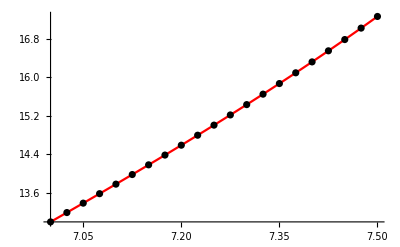

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.025; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h,y + k1];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2," y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + 1/2(k1+k2);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### в) Каква е теоретичната грешка на полученото приближено решение

Теоретична локална грешка: 0.000015625
Теоретична глобална грешка: 0.000625

### г) Каква би била точността при използване на модифицирания метод на Ойлер?

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 20. и стъпка h = 0.025

Теоретичната локална грешка  е 0.000015625

Теоретичната глобална грешка е 0.000625

i = 0 x_i = 7. y_i = 13. f_i = 7.74411 x_(i + 1/2) = 7.0125 y_(i + 1/2) = 13.0968 f_(i + 1/2) = 7.76593  y_точно = 13. Истинска грешка = 1.77636×10^-15

i = 1 x_i = 7.025 y_i = 13.1941 f_i = 7.78913 x_(i + 1/2) = 7.0375 y_(i + 1/2) = 13.2915 f_(i + 1/2) = 7.8132  y_точно = 13.1942 Истинска грешка = 8.04573×10^-6

i = 2 x_i = 7.05 y_i = 13.3895 f_i = 7.83872 x_(i + 1/2) = 7.0625 y_(i + 1/2) = 13.4875 f_(i + 1/2) = 7.86513  y_точно = 13.3895 Истинска грешка = 0.0000168608

i = 3 x_i = 7.075 y_i = 13.5861 f_i = 7.89307 x_(i + 1/2) = 7.0875 y_(i + 1/2) = 13.6848 f_(i + 1/2) = 7.92193  y_точно = 13.5861 Истинска грешка = 0.0000264839

i = 4 x_i = 7.1 y_i = 13.7842 f_i = 7.9524 x_(i + 1/2) = 7.1125 y_(i + 1/2) = 13.8836 f_(i + 1/2) = 7.98381  y_точно = 13.7842 Истинска грешка = 0.0000369553

i = 5 x_i = 7.125 y_i = 13.9837 f_i = 8.01692 x_(i + 1/2) = 7.1375 y_(i + 1/2) = 14.084 f_(i + 1/2) = 8.05099  y_точно = 13.9838 Истинска грешка = 0.0000483161

i = 6 x_i = 7.15 y_i = 14.185 f_i = 8.08686 x_(i + 1/2) = 7.1625 y_(i + 1/2) = 14.2861 f_(i + 1/2) = 8.12369  y_точно = 14.1851 Истинска грешка = 0.000060609

i = 7 x_i = 7.175 y_i = 14.3881 f_i = 8.16242 x_(i + 1/2) = 7.1875 y_(i + 1/2) = 14.4901 f_(i + 1/2) = 8.20213  y_точно = 14.3882 Истинска грешка = 0.000073878

i = 8 x_i = 7.2 y_i = 14.5932 f_i = 8.24383 x_(i + 1/2) = 7.2125 y_(i + 1/2) = 14.6962 f_(i + 1/2) = 8.28654  y_точно = 14.5933 Истинска грешка = 0.0000881685

i = 9 x_i = 7.225 y_i = 14.8003 f_i = 8.33132 x_(i + 1/2) = 7.2375 y_(i + 1/2) = 14.9045 f_(i + 1/2) = 8.37713  y_точно = 14.8004 Истинска грешка = 0.000103527

i = 10 x_i = 7.25 y_i = 15.0098 f_i = 8.42512 x_(i + 1/2) = 7.2625 y_(i + 1/2) = 15.1151 f_(i + 1/2) = 8.47415  y_точно = 15.0099 Истинска грешка = 0.000120003

i = 11 x_i = 7.275 y_i = 15.2216 f_i = 8.52545 x_(i + 1/2) = 7.2875 y_(i + 1/2) = 15.3282 f_(i + 1/2) = 8.57783  y_точно = 15.2218 Истинска грешка = 0.000137644

i = 12 x_i = 7.3 y_i = 15.4361 f_i = 8.63257 x_(i + 1/2) = 7.3125 y_(i + 1/2) = 15.544 f_(i + 1/2) = 8.6884  y_точно = 15.4362 Истинска грешка = 0.000156503

i = 13 x_i = 7.325 y_i = 15.6533 f_i = 8.7467 x_(i + 1/2) = 7.3375 y_(i + 1/2) = 15.7626 f_(i + 1/2) = 8.80611  y_точно = 15.6534 Истинска грешка = 0.000176633

i = 14 x_i = 7.35 y_i = 15.8734 f_i = 8.86809 x_(i + 1/2) = 7.3625 y_(i + 1/2) = 15.9843 f_(i + 1/2) = 8.9312  y_точно = 15.8736 Истинска грешка = 0.000198088

i = 15 x_i = 7.375 y_i = 16.0967 f_i = 8.99699 x_(i + 1/2) = 7.3875 y_(i + 1/2) = 16.2092 f_(i + 1/2) = 9.06392  y_точно = 16.0969 Истинска грешка = 0.000220925

i = 16 x_i = 7.4 y_i = 16.3233 f_i = 9.13364 x_(i + 1/2) = 7.4125 y_(i + 1/2) = 16.4375 f_(i + 1/2) = 9.20452  y_точно = 16.3235 Истинска грешка = 0.000245201

i = 17 x_i = 7.425 y_i = 16.5534 f_i = 9.2783 x_(i + 1/2) = 7.4375 y_(i + 1/2) = 16.6694 f_(i + 1/2) = 9.35325  y_точно = 16.5537 Истинска грешка = 0.000270976

i = 18 x_i = 7.45 y_i = 16.7872 f_i = 9.43122 x_(i + 1/2) = 7.4625 y_(i + 1/2) = 16.9051 f_(i + 1/2) = 9.51038  y_точно = 16.7875 Истинска грешка = 0.000298312

i = 19 x_i = 7.475 y_i = 17.025 f_i = 9.59267 x_(i + 1/2) = 7.4875 y_(i + 1/2) = 17.1449 f_(i + 1/2) = 9.67616  y_точно = 17.0253 Истинска грешка = 0.000327273

i = 20 x_i = 7.5 y_i = 17.2669 f_i = 9.76291 x_(i + 1/2) = 7.5125 y_(i + 1/2) = 17.3889 f_(i + 1/2) = 9.85087  y_точно = 17.2673 Истинска грешка = 0.000357923

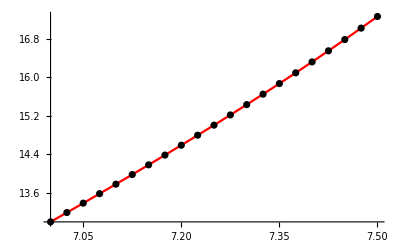

```mathematica
(*Въвеждаме услонието на задачата*)
a = 7.;b=7.5;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y - 8Sin[x]
(*Точно решение*)
yt[x_] := (13 ⅇ^x-4 ⅇ^x Cos[7]+4 ⅇ^7 Cos[x]-4 ⅇ^x Sin[7]+4 ⅇ^7 Sin[x])/ⅇ^7
(*Съставяме мрежата*)
h = 0.025; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```